-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 12 IV. Classical Statistical Mechanics

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

## IV.A General Definitions

```mathematica
(1) -- Statistical Mechanics uses probability to understand how the behavior of many tiny particles leads to the overall properties we can measure in large systems. It helps us connect the microscopic world to the macroscopic one we experience.
```

(2) -- Remember how we talked about equilibrium properties of big objects in the first chapter? Well, we can describe those using just a few thermodynamic coordinates. But to really understand what's going on, we need to look at all the tiny parts that make up these objects.

Now, each of these tiny parts has its own "micro-state," and there are a ton of them! It would take forever to describe each one. Instead of trying to follow each micro-state, we look at a whole bunch of them together. This group is called an ensemble, and it represents the overall "macro-state" of the object.

In statistical mechanics, we try to figure out how likely each micro-state is within this ensemble. There's this cool thing called Liouville's theorem that tells us that in equilibrium, all the micro-states that can happen are equally likely.

Remember, assigning these probabilities is kind of subjective, as we talked about in chapter III. But it helps us understand how all these tiny parts work together to create the big picture we see in thermodynamics.

```mathematica
(3) -- this chapter we shall provide unbiased estimates of $p_{M}(\mu)$ for a number of different equilibrium ensembles. A central conclusion is that in the thermodynamic limit of large $N$ all these ensembles are in fact equivalent. In contrast to kinetic theory, equilibrium statistical mechanics leaves out the question of how various systems achieve equilibrium.
```

## IV.B The Microcanonical Ensemble

```mathematica
(4) -- Let's talk about the microcanonical ensemble, which is our starting point in thermodynamics. Imagine a system that's completely isolated - no heat or work can get in or out. In this case, the system's energy (E) and its physical properties (x) stay constant. We call this combination of energy and properties a macro-state (M).

Now, even though the macro-state is fixed, there are many possible ways the particles in the system can arrange themselves while keeping the overall energy the same. These different arrangements are called micro-states, and the collection of all possible micro-states forms the microcanonical ensemble.

In classical physics, we can think of these micro-states as points in a special space called phase space. The behavior of these points over time is governed by something called a Hamiltonian (H(μ)). The Hamiltonian ensures that the total energy of the system stays constant, so all the micro-states are confined to a surface in phase space where H(μ) = E.

Assuming there's nothing else keeping the system from exploring all possible arrangements, the key idea in statistical mechanics is that each micro-state is equally likely to occur when the system is in equilibrium.
```

Statistical Mechanics
Ramirez (5)

```mathematica
MaTeX["p_{(E, \\mathbf{x})}(\\mu)=\\frac{1}{\\Omega(E, \\mathbf{x})} \\cdot \\begin{cases}1 & \\text {for} \\mathcal{H}(\\mu)=E \\\\ 0 & \\text {otherwise}\\end{cases}", Magnification -> 4]
```

-Graphics-

```mathematica
(6) -- Some remarks and clarification on the above postulate are in order:
```

(7) -- In thermodynamics and statistical mechanics, we often deal with systems containing a vast number of particles. To understand these systems, we use Boltzmann's assumption of equal a priori probabilities. This assumption states that all microstates with the same energy are equally likely to occur in an isolated system at equilibrium.

This idea is consistent with Liouville's theorem, which describes the conservation of phase space volume. The phase space represents all possible states of a system, with each point corresponding to a unique microstate μ. When we change our description of the system (μ → μ'), the volume in phase space remains unchanged. This transformation preserves the uniformity of probability distribution on the constant energy surface.

Understanding these concepts helps us connect the microscopic behavior of particles to the macroscopic properties we observe in thermodynamic systems.

## (2) The normalization factor

```mathematica
(8) -- (2) The normalization factor $\Omega(E, \mathbf{x})$, is the area of the surface of constant energy $E$ in phase space. To avoid subtleties associated with densities that are non-zero only a surface, is sometimes more convenient to define the microcanonical ensemble by requiring $E-\Delta \leq \mathcal{H}(\mu) \leq E+\Delta$, i.e. assigning the energy of the ensemble up to an uncertainty of $\Delta$. In this case, the accessible phase space forms a shell of thickness $\Delta$ around the surface of energy $E$. The normalization is now the volume of the shell, $\Omega^{\prime} \approx 2 \Delta \Omega$. Since $\Omega$ typically depends exponentially on $E$, as long as $\Delta \sim \mathcal{O}\left(E^{0}\right)$ (or even $\mathcal{O}\left(E^{1}\right)$ ), the difference between the surface and volume of the shell is negligible in the $E \propto N \rightarrow \infty$ limit, and we shall use $\Omega$ and $\Omega^{\prime}$ interchangeably.
```

## (3) The entropy of this uniform probability distribution

(9) -- In our study of uniform probability distributions, we encounter a fundamental concept: entropy. For a system with W equally probable microstates, the entropy S is expressed as:

S = k ln W

Here, k represents Boltzmann's constant. This equation quantifies the degree of disorder or randomness in the system. As the number of microstates increases, so does the entropy, reflecting a greater spread of possible configurations for the system.

Statistical Mechanics
Ramirez (10)

```mathematica
MaTeX["S(E, \\mathbf{x})=k_{B} \\ln \\Omega(E, \\mathbf{x})", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S(Ener, \\mathbf{x})=k_{B} \\ln \\Omega(Ener, \\mathbf{x})",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S[Ener,x]==k_B ln Ω[Ener,x]

(11) -- In thermodynamics, we use a special unit for entropy called energy per degree Kelvin. To make sure our calculations match this unit, we include an extra factor, Boltzmann's constant (kB), in our equation.

The entropy (S) and the number of possible states (Ω) don't change when we look at a system from different angles or use different coordinate systems. This is important because it means our calculations are consistent no matter how we approach the problem.

When we have multiple independent systems, we can find the total number of possible states by multiplying the individual possibilities together. This means the entropy of the whole system is simply the sum of the entropies of its parts. This additive property is exactly what we expect for extensive quantities in thermodynamics.

```mathematica
(12) -- Let's break this down into simpler terms. When we're dealing with big systems that have lots of moving parts, we can use a special equation (which we call equation IV.1) to figure out many important things about how heat and energy work. This equation is super useful because it helps us understand and predict what happens in these complex systems, especially when we're looking at them on a large scale. Think of it like having a magic formula that unlocks many secrets about how energy behaves in big, complicated setups.
```

## The Zeroth law:

(13) -- Let's explore the Zeroth Law of Thermodynamics through the lens of statistical mechanics. Imagine we have two separate systems that we bring together, allowing them to exchange energy but not work. If the initial energies of these systems are E₁ and E₂, their combined energy is simply E = E₁ + E₂.

When we join these systems, each possible state of the combined system is made up of a pair of states from the original systems. We can represent this mathematically as μ = μ₁ ⊗ μ₂, where ⊗ indicates the combination of states. The energy of this combined state is the sum of the energies of the individual states: H(μ₁ ⊗ μ₂) = H₁(μ₁) + H₂(μ₂).

In equilibrium, the combined system will be in a microcanonical ensemble with total energy E = E₁ + E₂. This approach allows us to understand equilibrium properties by examining how energy is distributed between the two systems.

Statistical Mechanics
Ramirez (14)

```mathematica
MaTeX["p_{E}\\left(\\mu_{1} \\otimes \\mu_{2}\\right)=\\frac{1}{\\Omega(E)} \\cdot \\begin{cases}1 & \\text {for} \\mathcal{H}_{1}\\left(\\mu_{1}\\right)+\\mathcal{H}_{2}\\left(\\mu_{2}\\right)=E \\\\ 0 & \\text {otherwise}\\end{cases}", Magnification -> 4]
```

-Graphics-

(15) -- Since only the overall energy is fixed, the total allowed phase space is computed from

Statistical Mechanics
Ramirez (16)

```mathematica
MaTeX["\\Omega(E)=\\int  \\Omega_{1}\\left(E_{1}\\right) \\Omega_{2}\\left(E-E_{1}\\right) \\,  d E_{1}=\\int  \\exp \\left[\\frac{S_{1}\\left(E_{1}\\right)+S_{2}\\left(E-E_{1}\\right)}{k_{B}}\\right]\\,  d E_{1}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Omega(Ener)=\\int  \\Omega_{1}\\left((Ener)_{1}\\right) \\Omega_{2}\\left((Ener)-(Ener)_{1}\\right) \\,  d(Ener)_{1}=\\int  \\exp \\left[\\frac{S_{1}\\left((Ener)_{1}\\right)+S_{2}\\left((Ener)-(Ener)_{1}\\right)}{k_{B}}\\right]\\,  dE_{1}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ω[Ener]==∫Ω_1[Ener_1] Ω_2[Ener-Ener_1]ⅆ Ener_1==∫exp[(S_1[Ener_1]+S_2[Ener-Ener_1])/k_B]ⅆ ⅇ_1

```mathematica
(17) -- When two systems come together and reach a new equilibrium, their properties are hidden within equation (IV.3). To better understand these properties, we need to look at the entropy described by equation (IV.4).

Now, here's an important concept: entropy is related to the number of particles in a system. This means that S₁ and S₂ (the entropies of the two systems) grow as the number of particles increases.

Because of this relationship, the expression inside the integral in equation (IV.4) becomes extremely large. This allows us to use a special mathematical trick called the saddle point method. Essentially, we can say that the integral is equal to the maximum value of what's inside it.

This maximum occurs at specific energy values, which we call E₁* and E₂*. Remember that the total energy E doesn't change, so E₂* is simply E minus E₁*.

By using this approach, we can figure out the exact energy distribution between the two systems in their new equilibrium state.
```

Statistical Mechanics
Ramirez (18)

```mathematica
MaTeX["S(E)=k_{B} \\ln \\Omega(E) \\approx S_{1}\\left(E_{1}^{*}\\right)+S_{2}\\left(E_{2}^{*}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S(E)=k_{B} \\ln \\Omega(E) \\approx S_{1}\\left(E_{1}^{*}\\right)+S_{2}\\left(E_{2}^{*}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(S[ⅇ]==k_B ln Ω[ⅇ])≈S_1[(ⅇ_1)^*]+S_2[(ⅇ_2)^*]

(19) -- To find where the maximum occurs, we need to look at the most important part of equation (IV.4). This is the exponent. We want to find the value of E₁ that makes this exponent as large as possible. 

To do this, we use a technique called extremization. It's like finding the peak of a mountain. We adjust E₁ until we reach the point where any small change would make the exponent smaller.

This process gives us a condition that tells us exactly where the maximum is located. It's a bit like finding the perfect balance point on a seesaw.

Statistical Mechanics
Ramirez (20)

```mathematica
MaTeX["\\left.\\frac{\\partial S_{1}}{\\partial E_{1}}\\right|_{\\mathbf{x}_{1}}=\\left.\\frac{\\partial S_{2}}{\\partial E_{2}}\\right|_{\\mathbf{x}_{2}}", Magnification -> 4]
```

-Graphics-

(21) -- Imagine we have two systems that can exchange energy. At first, you might think all possible energy arrangements are equally likely. But here's the cool part: there are way more ways for the energy to be divided close to a specific split (E₁*, E₂*) than any other.

When we let these systems interact, they start exploring different energy arrangements. We can't predict exactly how this happens or how long it takes. But after enough time passes, we can be almost certain that the energy will end up divided very close to (E₁*, E₂*).

At this point, something interesting occurs: a special condition is met that relates two important properties of the systems. These properties act like temperatures, and this relationship matches what we see in real-world thermodynamics experiments!

Statistical Mechanics
Ramirez (22)

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial E}\\right|_{\\mathbf{x}}=\\frac{1}{T}", Magnification -> 4]
```

-Graphics-

## The first law:

(23) -- Let's explore how the entropy S changes when we adjust the system's coordinates. Imagine we make a small change δx to the coordinates. This change does work on the system, equal to J · δx, where J is the generalized force. As a result, the system's internal energy increases by the same amount. Now, we can express the small change in entropy due to this adjustment:

ΔS = S(E + J · δx, x + δx) - S(E, x)

This relationship helps us understand how entropy varies with changes in the system's coordinates and energy.

Statistical Mechanics
Ramirez (24)

```mathematica
MaTeX["\\delta S=S(E+\\mathbf{J} \\cdot \\delta \\mathbf{x}, \\mathbf{x}+\\delta \\mathbf{x})-S(E, \\mathbf{x})=\\left(\\left.\\frac{\\partial S}{\\partial E}\\right|_{\\mathbf{x}} \\mathbf{J}+\\left.\\frac{\\partial S}{\\partial \\mathbf{x}}\\right|_{E}\\right) \\cdot \\delta \\mathbf{x}", Magnification -> 4]
```

-Graphics-

```mathematica
(25) -- When a system isn't in its most likely state, it will naturally change on its own. It's like a ball rolling downhill - it happens by itself. This change keeps happening until the system reaches its most probable state.

However, there's a special case where this spontaneous change doesn't occur. It's when a certain mathematical expression (which we put in brackets) equals zero.

We can use equation (IV.7) to figure out what these brackets mean in terms of derivatives. Derivatives help us understand how one thing changes when we change something else.

By understanding this, we can predict when and how systems will change on their own, which is super useful in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial x_{i}}\\right|_{E, x_{j \\neq i}}=-\\frac{J_{i}}{T}", Magnification -> 4]
```

-Graphics-

```mathematica
(27) -- Having thus identified all variations of $S$, we have
```

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["d S(E, \\mathbf{x})=\\frac{d E}{T}-\\frac{\\mathbf{J} \\cdot d \\mathbf{x}}{T}, \\quad \\Longrightarrow \\quad d E=T d S+\\mathbf{J} \\cdot d \\mathbf{x}", Magnification -> 4]
```

-Graphics-

(29) -- In thermodynamics, we often deal with systems that exchange heat with their surroundings. To understand these processes better, we use the concept of entropy, denoted by S. Entropy is a measure of the disorder or randomness in a system.

When a system receives heat, its entropy usually increases. We can express this relationship mathematically as:

dQ = T dS

Here, dQ represents the small amount of heat added to the system, T is the temperature of the system, and dS is the small change in entropy.

This equation tells us that the heat input (dQ) is directly proportional to both the temperature (T) and the change in entropy (dS). It's a fundamental relationship in thermodynamics that helps us analyze heat transfer processes and understand how systems evolve when they exchange energy with their surroundings.

## The second law:

(30) -- When we talk about systems reaching equilibrium, we're dealing with a lot of moving parts - imagine billions of tiny particles. With so many particles involved, it becomes super unlikely that the energy will be distributed in any way other than the most probable one. This most likely distribution is what we call equilibrium.

Think of it like this: if you shake a box of marbles, they'll settle into a certain pattern. The more marbles you have, the more certain you can be about how they'll end up arranged. In the same way, when we have a huge number of particles, we can be pretty sure about how their energy will be spread out at equilibrium.

The cool thing is, this equilibrium state actually has more possible ways to arrange the energy than the starting point did. It's like nature prefers the arrangement with the most options!

Statistical Mechanics
Ramirez (31)

```mathematica
MaTeX["\\Omega_{1}\\left(E_{1}^{*}, \\mathbf{x}_{1}\\right) \\Omega_{2}\\left(E_{2}^{*}, \\mathbf{x}_{2}\\right) \\geq \\Omega_{1}\\left(E_{1}, \\mathbf{x}_{1}\\right) \\Omega_{2}\\left(E_{2}, \\mathbf{x}_{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Omega_{1}\\left(E_{1}^{*}, \\mathbf{x}_{1}\\right) \\Omega_{2}\\left(E_{2}^{*}, \\mathbf{x}_{2}\\right) \\geq \\Omega_{1}\\left(E_{1}, \\mathbf{x}_{1}\\right) \\Omega_{2}\\left(E_{2}, \\mathbf{x}_{2}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ω_1[(ⅇ_1)^*,x_1] Ω_2[(ⅇ_2)^*,x_2]≥Ω_1[ⅇ_1,x_1] Ω_2[ⅇ_2,x_2]

```mathematica
(32) -- As systems naturally move towards more probable states, they tend to lose specific details about their initial conditions. This loss of information is permanent and goes hand in hand with an increase in entropy. Think of it like mixing paint colors - once mixed, you can't easily separate them back to their original states. This process reflects the fundamental tendency of systems to become more disordered over time.
```

Statistical Mechanics
Ramirez (33)

```mathematica
MaTeX["\\delta S=S_{1}\\left(E_{1}^{*}\\right)+S_{2}\\left(E_{2}^{*}\\right)-S_{1}\\left(E_{1}\\right)-S_{2}\\left(E_{2}\\right) \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta S=S_{1}\\left(E_{1}^{*}\\right)+S_{2}\\left(E_{2}^{*}\\right)-S_{1}\\left(E_{1}\\right)-S_{2}\\left(E_{2}\\right) \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

δ S==S_1[(ⅇ_1)^*]+S_2[(ⅇ_2)^*]-S_1[ⅇ_1]-S_2[ⅇ_2]≥0

```mathematica
(34) -- as required by the second law of thermodynamics. When the two bodies are first brought into contact, the equality in eq.(IV.6) does not hold. The change in entropy is such that
```

Statistical Mechanics
Ramirez (35)

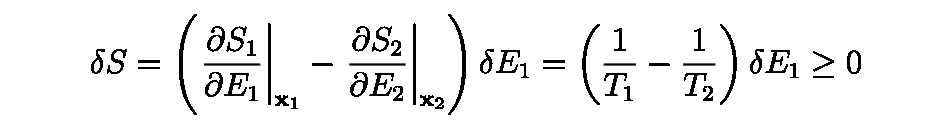

```mathematica
MaTeX["\\delta S=\\left(\\left.\\frac{\\partial S_{1}}{\\partial E_{1}}\\right|_{\\mathbf{x}_{1}}-\\left.\\frac{\\partial S_{2}}{\\partial E_{2}}\\right|_{\\mathbf{x}_{2}}\\right) \\delta E_{1}=\\left(\\frac{1}{T_{1}}-\\frac{1}{T_{2}}\\right) \\delta E_{1} \\geq 0", Magnification -> 4]
```

(36) -- Heat always moves from hot things to cold things. This is a fundamental rule in nature, known as the second law of thermodynamics. Imagine you have a hot cup of coffee and a cold glass of water. If you put them next to each other, heat will flow from the coffee to the water until they reach the same temperature. This process happens naturally and never reverses on its own. We can describe this idea mathematically using the concept of entropy, which measures the disorder in a system. As heat flows, the total entropy of the universe always increases, meaning things tend to become more disordered over time.

## Stability conditions:

(37) -- Let's think about stability in a simple way. When we talk about a maximum point, we're looking at the highest point on a curve. At this peak, the curve starts to bend downwards. In our case, we're dealing with the total entropy of two systems, S₁(E₁) + S₂(E₂). For this point to be stable, the curve must be bending downwards at (E₁*, E₂*). Mathematically, this means the second derivative of our entropy function should be negative at this point. This condition ensures that small changes in energy won't lead to a higher entropy state, keeping our system stable.

Statistical Mechanics
Ramirez (38)

```mathematica
MaTeX["\\left.\\frac{\\partial^{2} S_{1}}{\\partial E_{1}^{2}}\\right|_{\\mathbf{x}_{1}}+\\left.\\frac{\\partial^{2} S_{2}}{\\partial E_{2}^{2}}\\right|_{\\mathbf{x}_{2}} \\leq 0", Magnification -> 4]
```

-Graphics-

(39) -- Applying the above condition to two parts of the same system, the condition of thermal stability, $C_{\mathbf{x}} \geq 0$, as discussed in section (I.I), is regained. Similarly, the second order changes in eq.(IV.8) must be negative, requiring that the matrtix $\partial^{2} S /\left.\partial x_{i} \partial x_{j}\right|_{E}$ be positive definite.

## IV.C Two-Level Systems

```mathematica
(40) -- IV.C Two-Level Systems

Let's look at a simple system with N impurity atoms in a solid. Each impurity atom can be in one of two energy states: a low energy state (0) or a high energy state (ε). This system is different from what we've seen before because the energy states are discrete, not continuous. 

While Liouville's theorem typically applies to systems with continuous states, we can still use statistical mechanics principles here. The main idea is that all possible arrangements of these impurities (called microstates) should be equally likely over time. How exactly this happens isn't important right now, but we'll see an example using quantum mechanics later.

This simple two-level system helps us understand more complex systems in thermodynamics and statistical mechanics.
```

```mathematica
(41) -- The micro-states of the two level system are specified by the set of occupation numbers $\left\{n_{i}\right\}$, where $n_{i}=0$ or 1 depending on whether the $i^{\text {th }}$ impurity is in its ground state or excited. The overall energy is
```

Statistical Mechanics
Ramirez (42)

```mathematica
MaTeX["\\mathcal{H}\\left(\\left\\{n_{i}\\right\\}\\right)=\\epsilon \\sum_{i=1}^{N} n_{i} \\equiv \\epsilon N_{1}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{H}\\left(\\left\\{n_{i}\\right\\}\\right)=\\epsilon \\sum_{i=1}^{N} n_{i} \\equiv \\epsilon N_{1}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(H[{n_i}]==ϵ ∑_(i=1)^N n_i)≡ϵ N_1

(43) -- Let's think about a system with impurities that can be excited. N₁ represents how many of these impurities are actually excited. To describe the overall state of our system, we need to know two things: the total energy E, and the total number of impurities N. These two values define what we call the macro-state.

Now, in statistical mechanics, we're interested in the probability of finding the system in this particular macro-state. We call this the microcanonical probability. It tells us how likely it is to observe this specific combination of energy and impurities in our system.

Statistical Mechanics
Ramirez (44)

```mathematica
MaTeX["p\\left(\\left\\{n_{i}\\right\\}\\right)=\\frac{1}{\\Omega(E, N)} \\delta_{\\epsilon} \\sum_{i} n_{i}, E", Magnification -> 4]
```

-Graphics-

(45) -- Let's consider a system of impurities in a material. Some of these impurities can be excited, meaning they have a higher energy state. We have a total of N impurities, and E is the total energy in the system. Each excited impurity has an energy of ε (epsilon).

The number of excited impurities, which we call N₁, is equal to the total energy divided by the energy per impurity: N₁ = E / ε.

Now, we want to know how many different ways we can arrange these excited impurities among all the impurities. This is what we call the normalization, Ω (omega). It's essentially the number of ways to choose N₁ excited impurities out of the total N impurities.

We can calculate this using a concept from mathematics called the binomial coefficient. This gives us the number of ways to select a subset from a larger set.

This arrangement of excited impurities is crucial in understanding the system's behavior and its thermodynamic properties.

Statistical Mechanics
Ramirez (46)

```mathematica
MaTeX["\\Omega(E, N)=\\frac{N!}{N_{1}!\\left(N-N_{1}\\right)!}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Omega(E, N)=\\frac{N!}{N_{1}!\\left(N-N_{1}\\right)!}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ω[ⅇ,N]==(N!)/(N_1! (N-N_1)!)

```mathematica
(47) -- The entropy
```

Statistical Mechanics
Ramirez (48)

```mathematica
MaTeX["S(E, N)=k_{B} \\ln \\frac{N!}{N_{1}!\\left(N-N_{1}\\right)!}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S(E, N)=k_{B} \\ln \\frac{N!}{N_{1}!\\left(N-N_{1}\\right)!}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S[ⅇ,N]==(k_B ln N!)/(N_1! (N-N_1)!)

(49) -- In the realm of thermodynamics and statistical mechanics, we often encounter large numbers of particles. When dealing with systems where N₁ and N are much greater than 1, we can simplify our calculations using Stirling's formula. This approximation is particularly useful for factorial terms, which frequently appear in statistical mechanics equations. By applying Stirling's formula, we can more easily handle these large numbers and gain insights into the behavior of complex systems without getting bogged down in cumbersome calculations.

Statistical Mechanics
Ramirez (50)

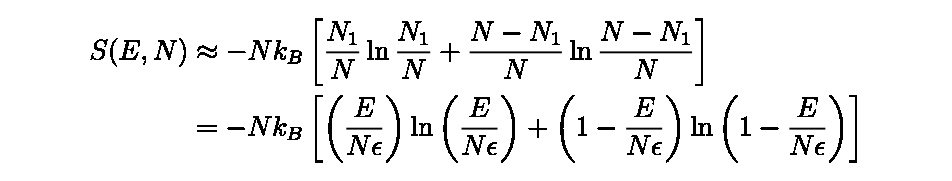

```mathematica
MaTeX["\\begin{aligned}S(E, N) & \\approx-N k_{B}\\left[\\frac{N_{1}}{N} \\ln \\frac{N_{1}}{N}+\\frac{N-N_{1}}{N} \\ln \\frac{N-N_{1}}{N}\\right] \\\\& =-N k_{B}\\left[\\left(\\frac{E}{N \\epsilon}\\right) \\ln \\left(\\frac{E}{N \\epsilon}\\right)+\\left(1-\\frac{E}{N \\epsilon}\\right) \\ln \\left(1-\\frac{E}{N \\epsilon}\\right)\\right]\\end{aligned}", Magnification -> 4]
```

(51) -- Let's calculate the equilibrium temperature using our earlier equation (IV.7). This temperature is the point where the system settles when left undisturbed. Think of it like the final temperature when you mix hot and cold water - it's somewhere in between. By using this equation, we can predict exactly what that final temperature will be, based on the properties of the system we're studying. This is a key concept in thermodynamics, helping us understand how energy is distributed in various systems at equilibrium.

Statistical Mechanics
Ramirez (52)

```mathematica
MaTeX["\\frac{1}{T}=\\left.\\frac{\\partial S}{\\partial E}\\right|_{N}=-\\frac{k_{B}}{\\epsilon} \\ln \\left(\\frac{E}{N \\epsilon-E}\\right)", Magnification -> 4]
```

-Graphics-

(53) -- Alternatively, the internal energy at a temperature $T$, is given by

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["E(T)=\\frac{N \\epsilon}{\\exp \\left(\\frac{\\epsilon}{k_{B} T}\\right)+1}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["E(T)=\\frac{N \\epsilon}{\\exp \\left(\\frac{\\epsilon}{k_{B} T}\\right)+1}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ⅇ[T]==(N ϵ)/(ⅇ^(ϵ/(k_B T))+1)

(55) -- Let's explore the fascinating world of internal energy and temperature in a two-level system. Imagine the internal energy as a function that always increases with temperature. It starts at zero when the temperature is absolute zero, and reaches its maximum value of Nε/2 when the temperature is infinitely high.

But here's where it gets interesting: we can actually have energies higher than Nε/2! When this happens, we enter the realm of negative temperatures. This might sound strange, but it's because as energy increases, there are fewer ways to arrange the system (fewer microstates). This is the opposite of what usually happens in most systems.

In a two-level system, there's a limit to how much energy it can have, and very few arrangements are possible near this maximum energy. So, oddly enough, more energy leads to more order in the system.

However, if we connect a negative temperature system to the rest of the universe (or any part of it that doesn't have an energy limit), it will lose its extra energy and settle at a positive temperature.

In the world of negative temperatures, things behave unusually. Adding heat can cool the system, while removing heat can warm it up! We can see examples of negative temperatures in some real-world situations, like in lasers or with magnetic spins, though these are temporary and not stable in the long term.

```mathematica
(56) -- The heat capacity of the system, given by
```

Statistical Mechanics
Ramirez (57)

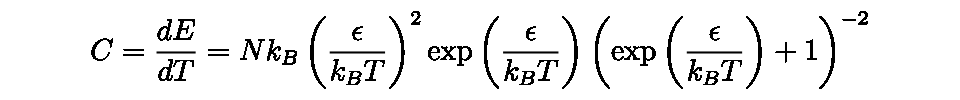

```mathematica
MaTeX["C=\\frac{d E}{d T}=N k_{B}\\left(\\frac{\\epsilon}{k_{B} T}\\right)^{2} \\exp \\left(\\frac{\\epsilon}{k_{B} T}\\right)\\left(\\exp \\left(\\frac{\\epsilon}{k_{B} T}\\right)+1\\right)^{-2}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["C=\\frac{d E}{d T}=N k_{B}\\left(\\frac{\\epsilon}{k_{B} T}\\right)^{2} \\exp \\left(\\frac{\\epsilon}{k_{B} T}\\right)\\left(\\exp \\left(\\frac{\\epsilon}{k_{B} T}\\right)+1\\right)^{-2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

C==dE/dT==(N k_B (ϵ/(k_B T))^2 ⅇ^(ϵ/(k_B T)))/((ⅇ^(ϵ/(k_B T))+1)^2)

(58) -- Let's explore how heat capacity behaves at different temperatures. At very low and very high temperatures, the heat capacity approaches zero. When temperatures are low, the heat capacity decreases exponentially, following the pattern e^(-ε/k_B T). This behavior is common in systems where there's an energy gap between the ground state and the first excited states. As we reach high temperatures, the heat capacity also drops to zero, which happens when the system can't absorb any more energy - it's saturated. Between these extremes, we observe a peak in heat capacity at a characteristic temperature proportional to ε/k_B. This pattern is typical for systems where the number of available energy states reaches a maximum at a certain energy level.

```mathematica
(59) -- Statistical mechanics gives us a powerful tool to understand how things work at both large and small scales. It's not just about big picture stuff like energy and how much heat something can hold.

When we look at equation (IV.16), we're actually looking at a map of all the possible ways tiny particles can behave. This map tells us a lot about what's happening at the smallest levels.

For instance, if we want to know how likely it is for a single particle to get excited, we can use this equation to figure that out. It's like having a crystal ball that lets us peek into the microscopic world!
```

Statistical Mechanics
Ramirez (60)

```mathematica
MaTeX["p\\left(n_{1}\\right)=\\sum_{\\left\\{n_{2}, \\cdots, n_{N}\\right\\}} p\\left(\\left\\{n_{i}\\right\\}\\right)=\\frac{\\Omega\\left(E-n_{1} \\epsilon, N-1\\right)}{\\Omega(E, N)}", Magnification -> 4]
```

-Graphics-

(61) -- When we have multiple impurities in a system, the energy gets distributed among them. If we know how much energy the first impurity takes, we can figure out how the rest of the energy is shared among the remaining impurities.

Think of it like sharing a cake. If you know how big a slice the first person takes, you can determine how much is left for everyone else.

We use equation (IV.17) to help us calculate this distribution. This equation gives us a mathematical way to describe how the energy is spread out among all the impurities except the first one.

By understanding this concept, we can better predict how energy behaves in systems with multiple impurities, which is crucial in many areas of thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (62)

```mathematica
MaTeX["p\\left(n_{1}=0\\right)=\\frac{\\Omega(E, N-1)}{\\Omega(E, N)}=\\frac{(N-1)!}{N_{1}!\\left(N-N_{1}-1\\right)!} \\cdot \\frac{N_{1}!\\left(N-N_{1}\\right)!}{N!}=1-\\frac{N_{1}}{N}", Magnification -> 4]
```

-Graphics-

(63) -- The probability of finding one particle in a specific energy state is given by N₁/N. Here, N₁ is the number of particles in that state, and N is the total number of particles.

We can express N₁ as E/ε, where E is the total energy and ε is the energy of a single particle in that state.

Using these relationships and the equation we derived earlier (eq.IV.21), we can determine the probability of particles occupying different energy states at a given temperature T.

This approach helps us understand how particles distribute themselves across various energy levels in a system at thermal equilibrium.

Statistical Mechanics
Ramirez (64)

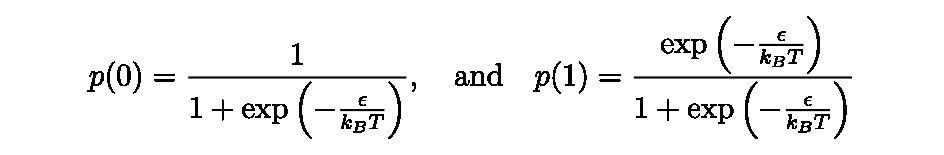

```mathematica
MaTeX["p(0)=\\frac{1}{1+\\exp \\left(-\\frac{\\epsilon}{k_{B} T}\\right)}, \\quad \\text {and} \\quad p(1)=\\frac{\\exp \\left(-\\frac{\\epsilon}{k_{B} T}\\right)}{1+\\exp \\left(-\\frac{\\epsilon}{k_{B} T}\\right)}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace[StringSplit["p(0)=\\frac{1}{1+\\exp \\left(-\\frac{\\epsilon}{k_{B} T}\\right)};; \\quad \\text {and} \\quad p(1)=\\frac{\\exp \\left(-\\frac{\\epsilon}{k_{B} T}\\right)}{1+\\exp \\left(-\\frac{\\epsilon}{k_{B} T}\\right)}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{p[0]==1/(1+ⅇ^(-ϵ/(k_B T))),and p[1]==ⅇ^(-ϵ/(k_B T))/(1+ⅇ^(-ϵ/(k_B T)))}

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear